```mathematica
fX[x_]:=4*x^3*Exp[-x^4/theta4]/theta4
delta[x_,t_]:=4/3*Pi*((c0*t+x)^3-(c1*t)^3)
```

```mathematica
Integrate[delta[x,t],{t,0,x/(c1-c0)}]
```

-(π x^4)/(3 c0)-(c1^3 π x^4)/(3 (c0-c1)^4)+(c1^4 π x^4)/(3 c0 (c0-c1)^4)

```mathematica
Integrate[Exp[-rho*mu*(-(π x^4)/(3 c0)-(c1^3 π x^4)/(3 (c0-c1)^4)+(c1^4 π x^4)/(3 c0 (c0-c1)^4))]*fX[x],{x,0,Infinity}]
```

ConditionalExpression[(12 (c0-c1)^3)/(12 (c0-c1)^3-4 (c0^2-3 c0 c1+3 c1^2) mu π rho theta4), ]

```mathematica
theta4=(3*c0)/(Pi*rho*mu)
```

(3 c0)/(mu π rho)

```mathematica
Simplify[(12 (c0-c1)^3)/(12 (c0-c1)^3-4 (c0^2-3 c0 c1+3 c1^2) mu π rho theta4)]
```

-(c0-c1)^3/c1^3

1

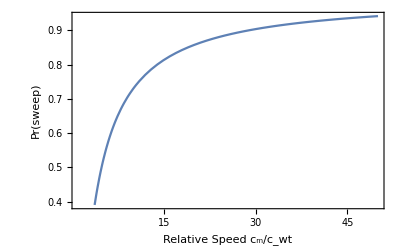

```mathematica
c0=1
Plot[-(c0-c1)^3/c1^3,{c1,1,50},Frame->True,FrameLabel->{Style["Relative Speed c_m/c_wt",Bold,12], Style["Pr(sweep)",Bold,12]}, RotateLabel->True]
```

```mathematica
Simplify[-rho*mu*(-(π x^4)/(3 c0)-(c1^3 π x^4)/(3 (c0-c1)^4)+(c1^4 π x^4)/(3 c0 (c0-c1)^4))]
```

((c0^2-3 c0 c1+3 c1^2) mu π rho x^4)/(3 (c0-c1)^3)